## Section | Atom-field interactions

To introduce atom-field interactions, we begin with the simplest setting: a single-mode field coupled to a two-level atom. In the semiclassical picture the atom is quantized while the field is treated classically. Under the dipole approximation, valid when the wavelength is much larger than the atomic size, the dynamics are analogous to a spin-1/2 in a time-dependent magnetic field, leading to optical Rabi oscillations. This semiclassical model captures basic oscillations, but fully quantizing the field reveals genuinely quantum phenomena such as “collapse and revival”. In this chapter we study the dynamics for several initial states and develop the tools used to analyze atom-field systems.

### Key Concepts

Semiclassical models

Rabi oscillations

Jaynes-Cummings model

Dressed state basis

### Atom-field interaction processes

We consider an atom with levels , with energies , where  denotes the lowest energy level, interacting with an electric field

### Absorption

Absorption occurs when an atom in a lower state transitions to a higher level and the amplitude of the electric field reduces. This is most relevant near resonance, 
ω ≃ ω_ba = (E_b-E_a/ℏ. For ω close to this transition frequency, the atom can be approximated as a two-level system.

### Stimulated emission

Stimulated emission is the counterpart of absorption and is also relevant near resonance. In this case an excited atom decays to a lower level and the field is amplified. Field amplification means that a photon is emitted with the same frequency, polarization, and phase as the incident field, so the fields interfere coherently.

### Spontaneous emission

Even in the absence of an electromagnetic field, an atom can decay from state |b⟩ to |a⟩, emitting a photon at the resonant frequency. The emitted photon has an arbitrary phase and polarization. We include this process for completeness, but its explanation requires a quantized field (all modes, including the vacuum).

Note: in the diagrams we are depicting photons because make the diagrams clearer, but the field that we will consider first is classical

### Semiclassical Hamiltonian models

The simplest semiclassical model considers a single electron bound to a stationary nucleus. The electron is quantized, while the field is classical and specified by the potentials A(r,t)  and U(r,t)

Using the Lagrangian formalism, one finds an interaction Hamiltonian that includes both the nuclear field and external fields:

Taking expectation values recovers the classical equations of motion. There are infinitely many potential pairs A(r,t), U(r,t) that produce the same electric and magnetic fields; moving between equivalent pairs is done via gauge transformations.

where F(r, t) is an arbitrary scalar field.

#### Coulomb gauge and A · p Hamiltonian

Thus there are infinitely many potentials  that reproduce the same electromagnetic field, all related by gauge transformations.

Imposing additional conditions fixes a gauge and removes the arbitrariness. A common choice in quantum optics is the Coulomb gauge, defined by:

This choice yields the transverse vector potential A_⊥(r,t ). For a plane electromagnetic wave, the Coulomb-gauge potentials  and  reproduce the E and B fields. The electric field is related to the vector potential by:

Consider an electron evolving under an external field and the nuclear Coulomb potential. For a plane-wave external field, the nuclear electrostatic field has zero vector potential and scalar potential . The semiclassical interaction Hamiltonian is:

Using the gauge condition, the Hamiltonian separates into two parts: H_0 is just , describing a charged particle in the Coulomb field, and H_I , the interaction of the external field with the hydrogen-like atom.

In atom-light interactions the wavelength λ is typically much larger than the atomic size. The external field amplitude can be taken as constant across the atom A_⊥(r_0, t); this is the long-wavelength (dipole) approximation. In this limit the vector potential is effectively constant.

The second term has vanishing matrix elements between different atomic states, so it cannot induce transitions and is discarded. The interaction Hamiltonian reduces to:

This is the “p · A Hamiltonian”, which uses the Coulomb gauge and evaluates the vector potential at the nucleus position.

#### Göppert-Mayer Gauge and electric dipole Hamiltonian

The Göppert-Mayer gauge is obtained by a gauge transformation of the Coulomb gauge with the following scalar field:

This transformation changes the potentials to:

The Hamiltonian then becomes:

Using the relation between the electric field and the vector potential, and introducing the operator D̂= q(r̂-r_0) , the Hamiltonian can be rewritten as:

Applying the long-wavelength approximation again, we replace A'(r̂,t) by A'(r_0,t). Using the transformed potentials gives A'(r_0,t)=0, and the Hamiltonian terms become:

This is the electric-dipole Hamiltonian, since it has the form of the interaction energy of a classical dipole located at r_0 in an electric field E.

Even if we have two different Hamiltonians , if we use exact equations and do not employ any additional approximation the predictions are the same regardless of the Hamiltonian choice . The long-wavelength approximation also predicts the same transition probabilities independent if A · p or D ·E is used . However, if extra approximations are used the results can differ depending on the specific problem, one Hamiltonian can provide more  accurate results to certain problems

### Atomic transitions: Rabi oscillations

With the semiclassical interaction Hamiltonian in hand, we can study transitions between atomic levels driven by a sinusoidally oscillating field. We first use first-order perturbation theory, then obtain a more accurate solution by restricting to a two-level atom near resonance.

#### Transition probabilities in first-order perturbation theory

Consider an atom with Hamiltonian H_0, eigenstates |j⟩ , and energies E_j. If the atom starts in eigenstate |i⟩  of H_0 and the driving field has frequency ω, we seek the probability of finding it in a different eigenstate |k⟩ at time t. We assume the interaction Hamiltonian applies beyond hydrogen, so we use the long-wavelength electric-dipole approximation.

Here D̂ has nonzero matrix elements between different eigenstates of H_0. Using the classical field expression, we write:

where

Using first-order perturbation theory for a sinusoidal drive of duration T, the transition probability from state |i⟩ to state |k⟩ is:

with W_(k i)is the matrix element and   the detuning (the absolute value treats both emission and absorption). The lineshape has a dominant peak of height T^2 centered at δ= 0

Visualize this function:

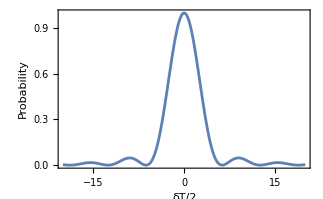

```mathematica
Plot[T^2(Sinc[δ T/2])^2 /. T->1,{δ,-20,20},PlotRange->Full,Frame->True,FrameLabel->{"δT/2","Probability"}]
```

To analyze the matrix element W_ik, we take the electric field as E(r_0) = ϵ E(r_0), where ϵ is a unit polarization vector.

Here d is the matrix element of the component of D̂ along the field direction. By adjusting the phases of the states |i⟩ and |k⟩, we can choose this matrix element to be real and negative, so we write:

where Ω_1 is said to be the Rabi frequency , and the transition probability takes the form:

This approach is limited to weak transitions, where the probability remains much smaller than unity.

#### Rabi oscillations between two levels

We now use a non-perturbative approach to compute the transition probability P_(i -> k) near resonance, with ω close to |E_k-E_i|/ℏ. In the two-level approximation, the states |a⟩ and |b⟩ have energies E_a, E_b. We set E_a = 0 and define the Bohr frequency ω_0  such that E_b-E_a = ℏ ω_0

The free Hamiltonian is:

Using the interaction Hamiltonian written in terms of the Rabi frequency, the total Hamiltonian is:

Used for simplifications:

```mathematica
$Assumptions = {t>0, δ>0 , Subscript[Ω, 1]>0,ω ∈ Reals,ν ∈ Reals};
```

Define an atomic basis:

```mathematica
atomBasis = QuantumBasis[{"a","b"}];
```

Define the atomic Hamiltonian (we take ℏ = 1):

```mathematica
atomicHamiltonian = h (QuantumOperator["X",atomBasis] Subscript[Ω, 1] Cos[ω t +ϕ]+QuantumOperator[DiagonalMatrix[{0,Subscript[ω, 0]}],atomBasis])
```

h Cos[ϕ+t ω] Ω_1ab+h Cos[ϕ+t ω] Ω_1ba+h ω_0bb

For a general initial state , the exponential factor accounts for free evolution:

```mathematica
ψi =QuantumState[{Subscript[c, a][t],Subscript[c, b][t] ⅇ^(-ⅈ Subscript[ω, 0] t)},atomBasis]
```

c_a(t)a+ⅇ^(-ⅈ t ω_0) c_b(t)b

The Schrodinger equation  :

```mathematica
schrodingerEq = (ⅈ D[ψi,t] - (atomicHamiltonian/h)@ψi)
```

(ⅈ c_a'(t)-Ω_1 ⅇ^(-ⅈ t ω_0) c_b(t) cos(t ω+ϕ))a+(Ω_1 c_a(t) (-cos(t ω+ϕ))+ⅈ (ⅇ^(-ⅈ t ω_0) c_b'(t)-ⅈ ω_0 ⅇ^(-ⅈ t ω_0) c_b(t))-ω_0 ⅇ^(-ⅈ t ω_0) c_b(t))b

We can get the resulting equations for c_a and c_b:

```mathematica
coefs =SolveValues[ Thread[schrodingerEq["AmplitudeList"]==0],{Subscript[c, a]'[t],Subscript[c, b]'[t]}][[1]]//TrigToExp
```

{-1/2 ⅈ Ω_1 c_b(t) ⅇ^(ⅈ t ω-ⅈ t ω_0+ⅈ ϕ)-1/2 ⅈ Ω_1 c_b(t) ⅇ^(-ⅈ t ω-ⅈ t ω_0-ⅈ ϕ),-1/2 ⅈ Ω_1 c_a(t) ⅇ^(ⅈ t ω+ⅈ t ω_0+ⅈ ϕ)-1/2 ⅈ Ω_1 c_a(t) ⅇ^(-ⅈ t ω+ⅈ t ω_0-ⅈ ϕ)}

Using the rotating-wave approximation (RWA), we drop the rapidly oscillating terms with exp(|ω + ω_0|). We define the detuning as δ = ω - ω_0.

Define rules to use RWA and replace the detuning:

```mathematica
RWAδrules ={ⅇ^(ⅈ ϕ + ⅈ t ω + ⅈ t Subscript[ω, 0])->0,ⅇ^(-ⅈ ϕ - ⅈ t ω - ⅈ t Subscript[ω, 0])->0,(ⅈ t ω-ⅈ t Subscript[ω, 0])-> ⅈ t δ,(ⅈ t Subscript[ω, 0]-ⅈ t ω)-> -ⅈ t δ};
```

Resulting equations:

```mathematica
eqs = Thread[{Subscript[c, a]'[t],Subscript[c, b]'[t]} == coefs /.RWAδrules]
```

{c_a'(t)==-1/2 ⅈ Ω_1 c_b(t) ⅇ^(ⅈ δ t+ⅈ ϕ),c_b'(t)==-1/2 ⅈ Ω_1 c_a(t) ⅇ^(-ⅈ δ t-ⅈ ϕ)}

Lets solve them for the case  (atom initially at the ground state) and introducing the variable Ω called generalized Rabi frequency:

```mathematica
coefSols = FullSimplify[DSolve[Join[eqs,{Subscript[c, a][0]== 1, Subscript[c, b][0] == 0}],{Subscript[c, a][t],Subscript[c, b][t]},t]] /.{√_->Ω,1/√_->1/ Ω}
```

{{c_a(t)→ⅇ^((ⅈ δ t)/2) (cos((t Ω)/2)-(ⅈ δ sin((t Ω)/2))/Ω),c_b(t)→-(ⅈ Ω_1 ⅇ^(-1/2 ⅈ (δ t+2 ϕ)) sin((t Ω)/2))/Ω}}

We can compute the probability that the atom initially in |a⟩ transitions to |b⟩ as a function of time, and plot it for different detunings

Wrap the solution as a QuantumState that depends on the parameters:

```mathematica
solvedState = QuantumState[Values @ coefSols[[1]],atomBasis,"Parameters"->{t,δ,Ω,Subscript[Ω, 1]}];
```

Extract the probability of finding the atom in the |b⟩ state:

```mathematica
probFuncs =(solvedState[t,#,√(1+#^2),1]["Probability"]["b"]& /@ Range[0,3] /. ϕ->0);
```

Plot the results:

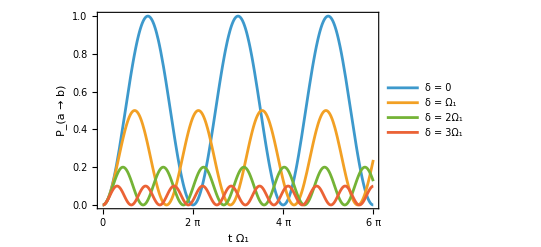

```mathematica
Plot[probFuncs,{t,0,6π},]
```

From the plot we see Rabi oscillations between 0 and the maximum value . As a function of ω, this maximum follows a Lorentzian profile: it peaks at zero detuning and has a full width at half maximum of 2Ω_1, which depends on the field amplitude.

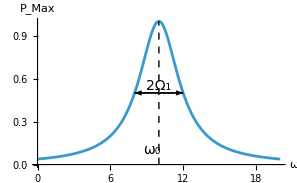

### Atom-field interaction (quantum model two level atom and single mode field)

With semiclassical models in place and the field now quantized, we can describe atom-field interactions fully quantum mechanically. The general multimode field and two-level atom Hamiltonian is:

Restricting to a single-mode field and a two-level atom, and applying the RWA to the interaction term, yields the Jaynes-Cummings Hamiltonian(JCH):

Annihilation operator (with automatic resizing), the field we will consider in the second qudit:

```mathematica
a := AnnihilationOperator[{2}]
```

Define the atomic basis and the truncation size:

```mathematica
SetFockSpaceSize[50];
atomBasis=QuantumBasis[{"e","g"}];
```

Define the transition operators  and :

```mathematica
σplus=QuantumOperator["+",atomBasis];
σminus=QuantumOperator["-",atomBasis];
```

Define the free Hamiltonian:

```mathematica
H0 = QuantumOperator[ 
h ν SuperDagger[a]@a+  1/2 h ω QuantumOperator["Z",atomBasis],
"Parameters"->{ν,ω}];
```

Define the atom-field interaction term:

```mathematica
H1 = h g (σplus@a +σminus@SuperDagger[a]);
```

Interaction-picture Hamiltonian:

```mathematica
HInteract = Simplify[MatrixExp[ⅈ H0/h t]@ H1 @ MatrixExp[-ⅈ H0/h t]];
```

At resonance this Hamiltonian is time independent:

```mathematica
FreeQ[HInteract[ν,ν]["AmplitudeList"],t]
```

True

So we can solve for the evolution operator Û:

```mathematica
U = MatrixExp[-ⅈ HInteract[ν,ν]/h t];
```

#### Solving JCH: Fock state as initial field state

With the time-evolution unitary in hand, we can evolve different initial states. We begin with the simplest case: a Fock state.

Build the state |g1⟩:

```mathematica
ψ0 = QuantumState["1",atomBasis]// FockState[1]
```

g1

Evolve the state:

```mathematica
ψt = U @ ψ0
```

-ⅈ sin(g t)e0+cos(g t)g1

Finding the probability of finding the atom in the excited state using a projection:

```mathematica
probE =((SuperDagger[QuantumState["0",atomBasis]]@ψt)["Norm"])^2
```

Abs[sin(g t)]^2

Plot as a function of  T = g t:

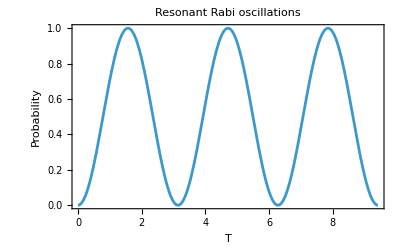

```mathematica
Plot[probE /. g->1 ,{t,0,3π},]
```

We recover the same resonant Rabi oscillations as in the semiclassical case; the oscillation frequency depends on which Fock state is evolved.

```mathematica
probs=  Table[{t,n,(SuperDagger[QuantumState["0",atomBasis]]@U@(QuantumState["1",atomBasis]// FockState[n]))["Norm"]},{n,4}];
ParametricPlot3D[Evaluate[probs/.g->1 ,{t,0,3π}],LabelStyle->14,PlotLabel->"Resonant Rabi oscillations",ImageSize->400,PlotLegends->{"|1⟩","|2⟩","|3⟩","|4⟩"},BoxRatios->{3,2,0.5}]
```

-Graphics3D-

#### Solving JC: coherent state as initial field state

Choose the initial state :

```mathematica
ψ0=QuantumState["1",atomBasis]//CoherentState[][5.]["Normalize"];
```

Compute the evolved state and the coefficients c_e(t) and c_g(t) for each n in the truncated Fock space.

Evolved state:

```mathematica
ψt=QuantumState[U@ψ0,"Parameters"->{g,t}];
```

Finding the time dependent  coefficients:

```mathematica
{cet[t_],cgt[t_]} = Values[(SuperDagger[#]@ψt[1,t])["Amplitudes"]& /@ atomBasis["BasisStates"]];
```

For any t, this returns a list (over all n) with length equal to the truncation size:

```mathematica
Length@cet[0] == $FockSize
```

True

Plot the population inversion computed from c_e(t ) and c_g(t). We observe collapse and revival, a phenomenon only present in the fully quantum model.

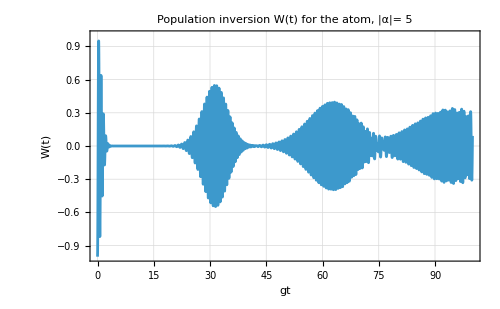

```mathematica
Plot[Evaluate[Total @(Abs[cet[t]]^2-Abs[cgt[t]]^2 )],{t,0,100},]
```

Evolution of the photon-number distribution:

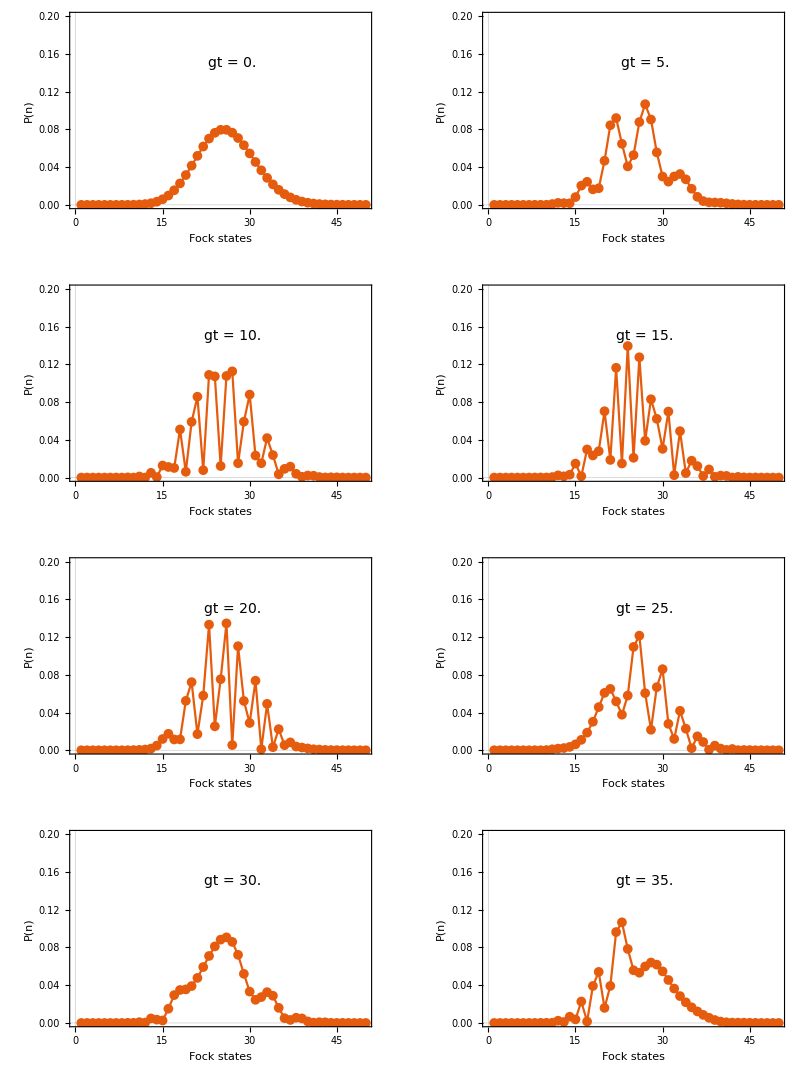

```mathematica
GraphicsGrid@Partition[Table[ListLinePlot[Evaluate[Abs[cet[t]]^2+Abs[cgt[t]]^2],],{t,Range[0,35,5]}],{2}]
```

At g t = 30, the distribution resembles the initial one; the revival is most pronounced around this time.

#### Density operator applied to thermal states

Now take the atom initially in the superposition  and the field in a thermal state (treated symbolically):

```mathematica
ρ0 = QuantumState["+",atomBasis]//ThermalState[x];
```

ρ_0 is a matrix-valued state:

```mathematica
ρ0["StateType"]
```

Matrix

Shortcut for matrix states to describe the evolution ρ(t) =Û(t) ρ(0) (Û)^†(t) :

```mathematica
ρt  = QuantumState[SuperDagger[U][ρ0],"Parameters"->{g,t}];
```

Extract the atomic density matrix:

```mathematica
atomMatrix = Normal[QuantumPartialTrace[ρt[1,t],{2}]["DensityMatrix"]]//ComplexExpand;
```

Plotting components, since the thermal state was evolved symbolically the value of x can be changed (of course such that can be represented in the chosen Fock space size):

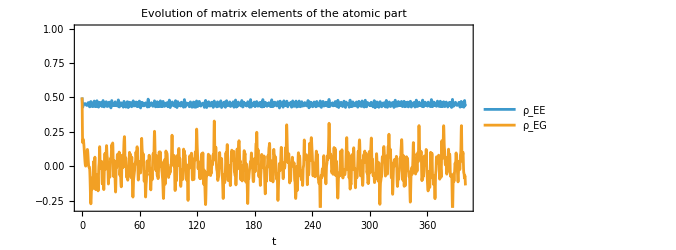

```mathematica
Plot[Evaluate[atomMatrix[[1,{1,2}]]/.x->4.],{t,0,400},]
```

The atom effectively thermalizes: the time-average of the coherences goes to 0.

Time average for one of the coherences:

```mathematica
timeAverages = Integrate[Evaluate[(atomMatrix[[1,2]]/.x->5.)],{t,0,tf}]/tf;
```

Plot the time averages:

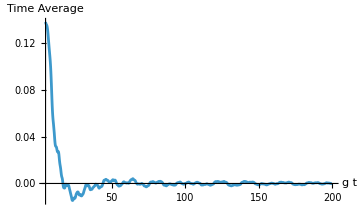

```mathematica
Plot[timeAverages,{tf,5,200},]
```

Compute the atomic inversion  after tracing out the Fock states. We evaluate it for an initially excited atom and a thermal field with n^— = 5.

Redoing the evolution for the state with the atom in the excited state:

```mathematica
ρ0 = QuantumState["0",atomBasis]//ThermalState[5.];
ρt  = QuantumState[SuperDagger[U][ρ0],"Parameters"->{g,t}];
atomMatrix = Normal[QuantumPartialTrace[ρt[1,t],{2}]["DensityMatrix"]];
```

Plot the atomic inversion:

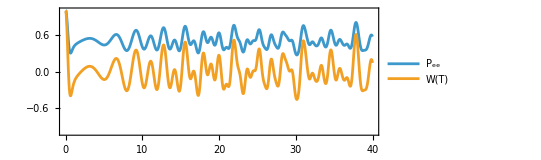

```mathematica
With[{ρe= atomMatrix[[1,1]]},Plot[{ρe,2ρe-1},{t,0,40},]]
```

### Dressed states

Work in a smaller truncation size:

```mathematica
SetFockSpaceSize[12];
```

Returning to the Jaynes-Cummings model, we separate the free and interaction terms:

```mathematica
H0 = QuantumOperator[h ν SuperDagger[a]@a+ 1/2 h ω QuantumOperator["Z",atomBasis],"Parameters"->{ν,ω}];
```

```mathematica
H1 = h g  (σplus@a+σminus@SuperDagger[a]);
```

For a fixed n, the dynamics is confined to the product states |e⟩|n⟩, |g⟩|n+1⟩ (or |e⟩|n-1⟩, |g⟩|n⟩). Near resonance (ν≃ ω), each pair is nearly degenerate. For a given n, the bare states are defined as:

Bare states implementation:

```mathematica
bareState[i_Integer,n_Integer/; 0<=n<= $FockSize-1]:=atomBasis["BasisStates"][[i+1]]//FockState[n+i]
```

Check for n=10:

```mathematica
{bareState[1,10],bareState[0,10]}
```

{g11,e10}

Under the free Hamiltonian the bare states are uncoupled, and their energy difference is set by the detuning h Δ (Δ = ν - ω).

Calculating the energy differences of the bare states for the same n:

```mathematica
Differences/@( Table[(H0 @ bareState[m,n])["AmplitudeList"][[1]],{n,0,$FockSize-2},{m,0,1}])
```

{{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω},{h ν-h ω}}

The matrix elements for a given  n of the bare states are (ℋ^(n))_ij are:

Compute the matrix elements:

Check ℋ_00:

```mathematica
Table[(bareState[0,n]["Dagger"] @ (H0+H1) @ bareState[0,n])["Scalar"],{n,0,$FockSize-2}]==Array[Expand[h(# ν + 1/2 ω)]&,$FockSize-1,0]
```

True

Check ℋ_11:

```mathematica
Table[(bareState[1,n]["Dagger"] @ (H0+H1) @ bareState[1,n])["Scalar"],{n,0,$FockSize-2}]== Array[Expand[h((#+1) ν - 1/2 ω)]&,$FockSize-1,0]
```

True

Check ℋ_01:

```mathematica
Table[(bareState[0,n]["Dagger"] @ (H0+H1) @ bareState[1,n])["Scalar"],{n,0,$FockSize-2}]== Array[Expand[h(g √(#+1))]&,$FockSize-1,0]
```

True

With these matrix elements we form the 2x2 dynamical matrix (from the interaction term) for a fixed n:

Dressed subspace operator:

```mathematica
dressedSubspace = QuantumOperator[{{h(n ν +1/2  ω),h g √(n+1)},{h g √(n+1), h((n+1) ν -1/2 ω)}}]
```

h (n ν+ω/2)00+g h √(1+n)01+g h √(1+n)10+h ((1+n) ν-ω/2)11

Calculate the eigenvalues (express in terms of the detuning):

```mathematica
eigenvals =ReplaceAll[#,{(ν-ω)->Δ}]& /@(dressedSubspace["Eigenvalues"])
```

{1/2 h (-√(Δ^2+4 g^2 (n+1))+ν+2 ν n),1/2 h (√(Δ^2+4 g^2 (n+1))+ν+2 ν n)}

The interaction Hamiltonian produces an energy shift hΩ_n(Δ) (when g = 0 there is no interaction and we recover the uncoupled result) Ω_n(Δ) = √(4g^2(n+1) + Δ^2) (generalized Rabi frequency). This energy splitting is also called AC Stark Shift

Calculate energy shift:

```mathematica
eigenvals//Differences //Simplify
```

{h √(Δ^2+4 g^2 (n+1))}

The eigenstates associated with these energies have the form:

such that

and   ,

Calculate the eigenvectors, and re-express the variables:

```mathematica
eigenVecs = FullSimplify[(dressedSubspace["Eigenvectors"]//. {ν-ω->Δ,-ν+ω->-Δ,√(4 g^2 (1+n)+Δ^2)->Subscript[Ω, n]}) ,Element[{Subscript[Ω, n],g,n,Δ},Reals] && Subscript[Ω, n]>Δ>0 && n>=0 && g>0 ];
```

"Eigenvectors"  yields an equivalent set of eigenvectors, for example {-cos(Φ), sin(Φ)} and {sin(Φ), cos(Φ)}:

```mathematica
simplifiedDressedEigenvecs = FullSimplify[#/.{ 1/(g^2(n+1))->4/( Subscript[Ω, n]^2-Δ^2), 4 g^2(n+1)->Subscript[Ω, n]^2-Δ^2 },Subscript[Ω, n]>0 && Δ>0]& /@ eigenVecs //Together
```

{{-(√((Δ+Ω_n)/Ω_n))/(√2),1/(√2 √(Ω_n/(-Δ+Ω_n)))},{(√((-Δ+Ω_n)/Ω_n))/(√2),(√((Δ+Ω_n)/Ω_n))/(√2)}}

When Δ = 0 the bare states are degenerate , but the splitting remains :

```mathematica
dressedSubspace["Eigenvalues"]/. ν->ω //Differences//Simplify
```

{2 h √(g^2 (n+1))}

In this limit the dressed states relate to the bare states as:

Test that limit(we negate first components to follow the literature convention):

```mathematica
MapAt[-#&,simplifiedDressedEigenvecs /. Δ->0,{{1,1},{2,1}}]
```

{{1/(√2),1/(√2)},{-1/(√2),1/(√2)}}

The dressed states are stationary states of the atom-field system, so the evolution can be written in this basis as:

### Schmidt decomposition and von Neumann entropy for Jaynes-Cummings

Any bipartite system admits a Schmidt decomposition; the general time-dependent state in the bare basis is:

Using the Schmidt decomposition, for any time we can find bases {|u_i(t)⟩} for the atom and {|v_i(t)⟩} for the field such that:

In those bases, the reduced density matrices of the atom and the field are identical:

Analytical form of the reduced atomic density matrix:

Using the Bloch-vector parametrization of the density matrix, we obtain the relations:

Arbitrary state specified as a 2x2 density matrix :

```mathematica
state = QuantumState[{{Subscript[b, 11],Subscript[b, 12]},{Subscript[b, 21],Subscript[b, 22]}}];
```

```mathematica
state["DensityMatrix"]//MatrixForm
```

(b_11 | b_12
b_21 | b_22)

Bloch vector expressed in terms of the components of the matrix:

```mathematica
state["BlochVector"]
```

{b_12+b_21,ⅈ b_12-ⅈ b_21,b_11-b_22}

The g coefficients are then expressed in terms of the Bloch-vector length.

Von Neumann entropy for each subsystem:

Return to the previous Fock space size:

```mathematica
SetFockSpaceSize[50];
```

Initial state (atom excited, field in a coherent state with |α|=5):

```mathematica
ψ0 = QuantumState["0",atomBasis]//CoherentState[][5.]["Normalize"];
```

Evolved state:

```mathematica
ψt = QuantumState[(U@ψ0),"Parameters"->{g,t}];
```

Bloch vector of the reduced density matrix:

```mathematica
blochVector =QuantumPartialTrace[U@ψ0,{2}]["BlochVector"] /. g t->T;
```

Plot of the s_i components (s_1 is zero for this given initial state  and and s_3 corresponds to the atomic population inversion) :

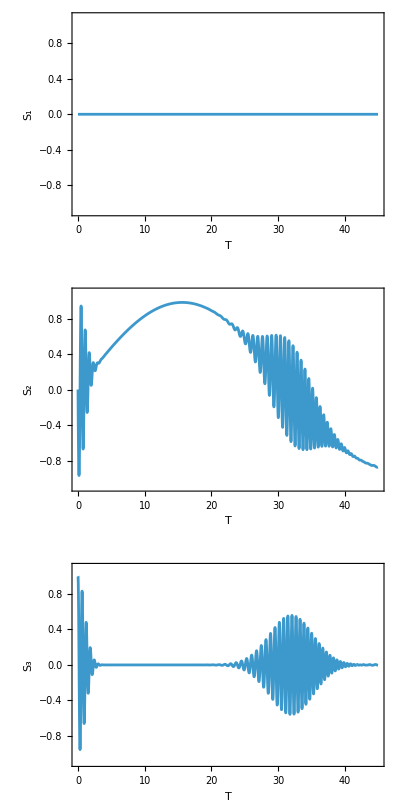

```mathematica
Labeled[GraphicsColumn[Table[Plot[blochVector⟦i⟧,{T,0,45},],{i,3}]],,Top]
```

Norm of the Bloch vector:

```mathematica
normBloch = Norm[blochVector];
```

Extracting the g coefficients:

```mathematica
{g1,g2}= {1/2(1+normBloch),1/2(1-normBloch)};
```

Calculating the Von Neumann entropy:

```mathematica
vonneumann= -g1 Log[g1]-g2 Log[g2];
```

Plot the entropy as a function of time:

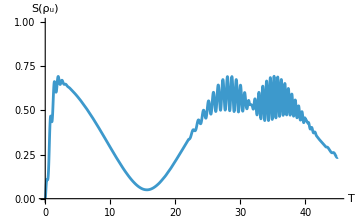

```mathematica
Plot[vonneumann ,{T,0,45},PlotRange->{0,1},AxesLabel->{"T","S(ρ_u)"},LabelStyle->12]
```

The Wolfram Quantum Framework provides the “SchmidtBasis” and “SchmidtDecompose” properties for quantum states.

Verify that g1 and g2 match the amplitudes from “SchmidtBasis” at a chosen time:

```mathematica
√({g1,g2} /. T->2.4)
```

{0.798282,0.602284}

```mathematica
ψt[1,2.4]["SchmidtBasis"]
```

0.798282u_1 v_1+0.602284u_2 v_2

Get the reduced density matrices in this basis:

```mathematica
Table[QuantumPartialTrace[ψt[1,2.4]["SchmidtBasis"],{i}],{i,2}];
```

Check that in this basis both have equivalent forms:

```mathematica
%//TraditionalForm
```

{0.637254v_1v_1+0.362746v_2v_2,0.637254u_1u_1+0.362746u_2u_2}

We can also compute "VonNeumannEntropy" directly for a QuantumState, obtaining the same result as before:

Atomic part of the evolved state:

```mathematica
evol = QuantumState[QuantumPartialTrace[U@ψ0,{2}],"Parameters"->{g,t}];
```

Plot “VonNeumannEntropy”:

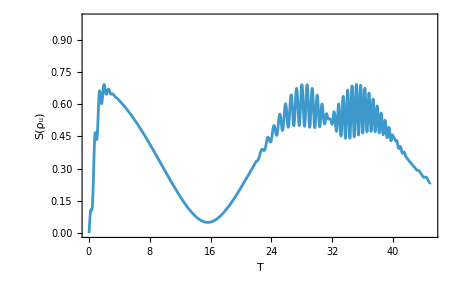

```mathematica
Plot[evol[1,t]["VonNeumannEntropy"]Log[2],{t,0,45},PlotRange->{0,1},Frame->True,FrameLabel->{"T","S(ρ_u)"},LabelStyle->14]
```

Function to minimize:

```mathematica
func[t_?NumericQ]:=QuantityMagnitude[evol[1,t]["VonNeumannEntropy"]Log[2]]
```

Finding the time of the local minimum of entropy:

```mathematica
Tmin =FindMinimum[func[t],{t,5}][[2]]
```

{t→15.654}

The maximum of s_2 corresponds to a minimum of the von Neumann entropy. This occurs when the reduced density matrices of the atom-field system are approximately pure (for this example, around T = gt ≃ 15.6).

Use the “Purity” property at the calculated time:

```mathematica
Table[QuantumPartialTrace[ψt[1,t/.Tmin],{i}]["Purity"],{i,2}]
```

{0.982672,0.982672}

##### Initialization

Load the Quantum Framework:

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Load the second quantization tools:

```mathematica
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```

Exercises

Define using the Quantum Framework a modified Jaynes-Cummings Hamiltonian, such that the atom has three levels, two ground states and one excited state. Find the state ψ(t) as a function of time for the initial state 1/(√3)(|e⟩ + |g_1⟩ + |g_2⟩ ) ⊗ |1⟩

Solution

Define the field truncation size and the annihilation operator:

SetFockSpaceSize[30];
a := AnnihilationOperator[{2}]

Define the new basis:

atomBasis = QuantumBasis[{"e","g_1","g_2"}];

Modified atomic transition operators:

σplus =QuantumOperator[PadRight[{{0,1,1}},{3,3}],atomBasis];
σminus = σplus^†;

Column[{σplus,σminus}]//TraditionalForm

"e""g_1"+"e""g_2"
"g_1""e"+"g_2""e"

Free Hamiltonian:

H0 = QuantumOperator[ 
h ν a^†@a+  1/2 h ω QuantumOperator[DiagonalMatrix[{1,-1,-1}],atomBasis],
"Parameters"->{ν,ω}];

Interaction part:

H1 = h g (σplus@a +σminus@a^†);

Going to the interaction picture:

HInteract = Simplify[MatrixExp[ⅈ H0/h t]@ H1 @ MatrixExp[-ⅈ H0/h t]];

Finding the unitary operator:

U = MatrixExp[-ⅈ HInteract[ν,ν]/h t];

Evolve the requested state:

Simplify@U[QuantumState[1/(√3){1,1,1},atomBasis]//FockState[1]]

-ⅈ √(2/3) sin(√2 g t)"e"0+(cos(2 g t))/(√3)"e"1+(cos(√2 g t))/(√3)"g_1"1-(ⅈ sin(2 g t))/(√6)"g_1"2+(cos(√2 g t))/(√3)"g_2"1-(ⅈ sin(2 g t))/(√6)"g_2"2

Following on the previous exercise, using this model find the dark states of the atom-field system. This amounts to finding states ψ such that H_I |ψ⟩ = 0

Solution

Find the eigensystem of the interaction Hamiltonian:

{vals,vecs}=N[HInteract]["Eigensystem"];

Show the possible dark states:

TraditionalForm[QuantumState[#,{atomBasis,$FockSize}]&/@Extract[vecs,Position[vals,0]]]

{-0.707107"g_1"29+0.707107"g_2"29,-0.707107"g_1"28+0.707107"g_2"28,-0.707107"g_1"27+0.707107"g_2"27,-0.707107"g_1"26+0.707107"g_2"26,-0.707107"g_1"25+0.707107"g_2"25,-0.707107"g_1"24+0.707107"g_2"24,-0.707107"g_1"23+0.707107"g_2"23,-0.707107"g_1"22+0.707107"g_2"22,-0.707107"g_1"21+0.707107"g_2"21,-0.707107"g_1"20+0.707107"g_2"20,-0.707107"g_1"19+0.707107"g_2"19,-0.707107"g_1"18+0.707107"g_2"18,-0.707107"g_1"17+0.707107"g_2"17,-0.707107"g_1"16+0.707107"g_2"16,-0.707107"g_1"15+0.707107"g_2"15,-0.707107"g_1"14+0.707107"g_2"14,-0.707107"g_1"13+0.707107"g_2"13,-0.707107"g_1"12+0.707107"g_2"12,-0.707107"g_1"11+0.707107"g_2"11,-0.707107"g_1"10+0.707107"g_2"10,-0.707107"g_1"9+0.707107"g_2"9,-0.707107"g_1"8+0.707107"g_2"8,-0.707107"g_1"7+0.707107"g_2"7,-0.707107"g_1"6+0.707107"g_2"6,-0.707107"g_1"5+0.707107"g_2"5,-0.707107"g_1"4+0.707107"g_2"4,-0.707107"g_1"3+0.707107"g_2"3,-0.707107"g_1"2+0.707107"g_2"2,-0.707107"g_1"1+0.707107"g_2"1,1."g_2"0,1."g_1"0,1."e"29}

So the requested state has the form 1/(√2)(|g_1⟩ - |g_2⟩) ⊗ |n⟩, for n ≥ 1:

With[{n= RandomInteger[{1,$FockSize-1}]},HInteract[QuantumState[1/(√2){0,1,-1}]//FockState[n]]]

0

Consider the atom-field Hamiltonian  without using the rotating wave approximation, this means keeping also terms that are not energy preserving (σ_x is used). Use values of strong coupling ω_c/g ≈ 0.5  , initial state |e,0⟩  and plot the concurrence and the Rabi oscillations as function of time. Also visualize the Wigner function of the field system at times when there is high atom-field entanglement.

Solution

Define the atomic basis:

atomBasis = QuantumBasis[{"e","g"}];

σplus = QuantumOperator["+",atomBasis];
σminus = QuantumOperator["-",atomBasis];

Define the Hamiltonian:

H =QuantumOperator[ωc a^†@a+ ωr/2 QuantumOperator["Z",atomBasis]+ g QuantumTensorProduct[QuantumOperator["X",atomBasis],a+a^†],"Parameters"->{ωc,ωr,g}];

Initial state:

ψ0 = QuantumState["0",atomBasis]//FockState[0];

Numerical evolution:

evolved =QuantumEvolve[H[1.,0.9,0.5],ψ0,{t,0,50}];

Concurrence plot:

Plot[QuantumEntanglementMonotone[evolved[t],{{1},{2}}],{t,0,50}]

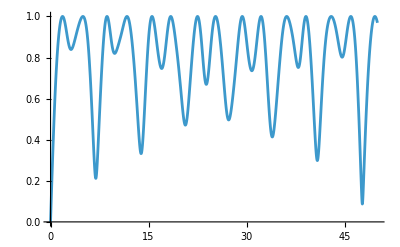

“Rabi” oscillations:

Plot[QuantumPartialTrace[evolved[t],{2}]["DensityMatrix"][[1,1]],{t,0,50}]

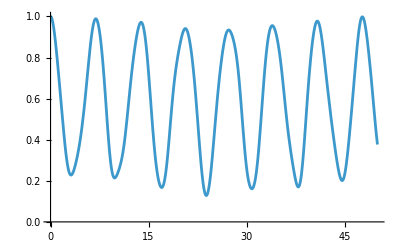

Phase space plots:

plots =Table[wig = WignerRepresentation[QuantumPartialTrace[evolved[t],{1}],{-4,4},{-4,4}];
DensityPlot[wig[x,p],{x,-4,4},{p,-4,4},PlotPoints->80,PlotRange->All,ColorFunction->"SolarColors",FrameLabel->{"x","p"},PlotLegends->Placed[Automatic, Top]],{t,{1.7,5.2,8.8,11.5}}];

Grid@Partition[plots,2]

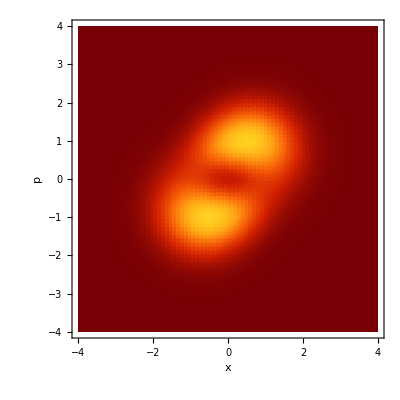
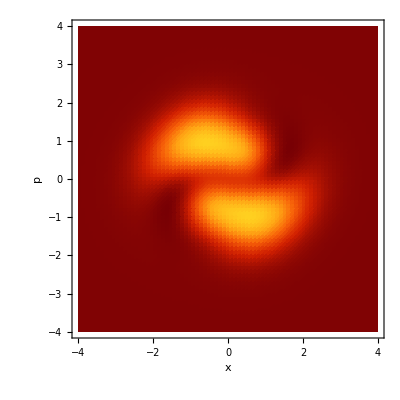
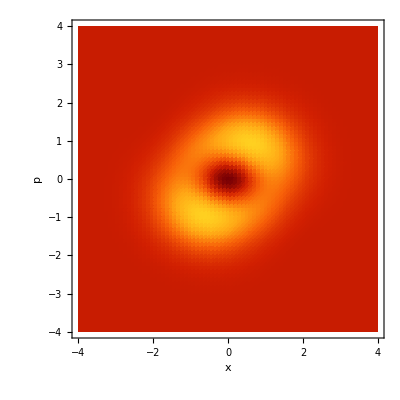
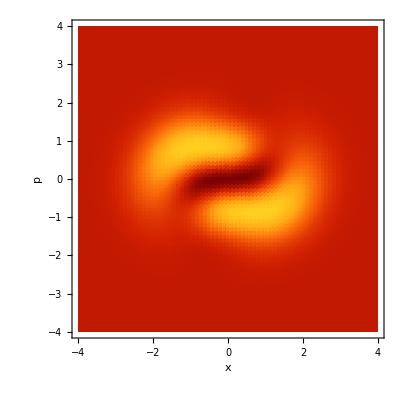
-Graphics- | -Graphics-
-Graphics- | -Graphics-